This script was written by Michele Kelley of University of North Carolina - Chapel Hill in 2020

To use this script, the best approach to use the menu Evaluation -> Evaluate Notebook and then use a separate notebook to use the functions. See examples of usage below.

# SpinExchange

Evaluates the Rb-Xe spin-exchange cross section

# XePolarization

Evaluates the Xe polarization from continuous-flow and stopped-flow spin-exchange optical pumping.

## Usage

fs[T,G]
		evaluates the fraction of interactions in the very-short lifetime regime

	SpinExchange[Xe, N2, He,T,G,PRb]
		evalutes the Xe polarization given the provided parameters

	XePolarization[Xe, N2, He,T, G,PRb,nRb,SD,V,slm,tc]
		evalutes the continous flow Xe polarization given the provided parameters

## Parameters

Xe: fraction of gas mixture that is xenon (ex. 0.01)
N2: fraction of gas mixture that is nitrogen (ex. 0.10)
He: fraction of gas mixture that is helium (ex. 0.89)
T: gas temperature in K (ex. 383)
G: gas density in amagats (ex. 3.5)
PRb: the polarization of Rb (ex. 0.80)
nRb: the Rb vapor density in m^-3 (ex. 4*10^18)
SD: the spin destruction rate (ex. 0.003)
V: the volume of the optical pumping cell in liters (ex. 0.270)
slm: the gas flow rate in standard liters per minute (ex. 0.75)
tc: the collection time in minutes (ex. 25)

## Definitions

Note [G]_1 is defined for a He dominate mixture, for other mixtures the temperature dependence should remain the same, but the constant should change (2.8 here). We think that one could use the values of p_o from Table III to estimate  [G]_1 of other mixtures as according to Nelson (2001) [G]_1/ [G]_0=28.7 (at 80 C - this is based off of γN/h=135 MHz and the relative hyperfine splitting of Rb, which should not depend on third body gas species) and p_o∝ [G]_o. Therefore a Xe dominate mixture should have an approximate [G]_1(Xe)= (p_o(He))/(p_o(Xe)) [G]_1(He)≈ 175/27*2.8 = 18. This would imply that Xe dominate mixtures stay in the short regime at relatively higher densities than He (or N_2).

```mathematica
(*THESE CONSTANTS MAY BE CHANGED IF NEW VALUES ARE REPORTED*)
σν=10*10^-22(*s^-1 m^3; binary collision spin-exchange cross section between Rb and Xe; Shao 2005*);
γM = 10.2*10^4 (*s^-1; Subscript[γ, M] for van der Waals spin-exchange; Shao 2005*);
T1solid = 87(*min; Subscript[T, 1] of solid Xe during cyrogenic collection; Norquay 2013*);
G1[T_, Xe_,N2_,He_]:=2.8(175/27*Xe+175/107*N2+He)(353/T)^2; (*amg; characteristic density in amagat; defines transition from short to very-short lifetime based off for a gas mixture 2.8 t 80 C and 1.95 at 150 C, expects T^-2 dependence; Nelson 2001; Nelson's work was for He dominate mixture - here we have scaled their results by characteristics pressures from Ramsey 1983*)
bN2[T_]:=28.3/107*(349/T)^(1/2); (*Subscript[b, Subscript[N, 2]]; Ramsey 1983 and Cates 1992*)
bHe[T_]:= 28.3/175*(349/T)^(1/2);(*Subscript[b, He]; Ramsey 1983 and Cates 1992*)
```

```mathematica
(*THESE SHOULD NOT BE ALTERED*)
amg=2.6867811×10^25; (*convert amagats to m^-3*)
i85 = 0.7215; (*isotopic abundance of^85 Rb*)
i87 = 0.2785; (*isotopic abundance of^87 Rb*)
HFratio=2.25; (*ratio of hyperfine frequecies of^85 Rb and^85 Rb*)
Z85[β_] := Exp[(-5/2)*β] + Exp[(-3/2)*β] + Exp[(-1/2)*β] + Exp[(5/2)*β] + Exp[(3/2)*β] + Exp[(1/2)*β]; (*spin temperature partition function for^85 Rb*)
Z87 [β_]:= Exp[(-3/2)*β] + Exp[(-1/2)*β] + Exp[(1/2)*β] + Exp[(3/2)*β];(*spin temperature partition function for^87 Rb*)
Ffunc85[b_]:= (1/2+5/2(5/2+1)-1/Z85[β] D[D[Z85[β],β],β])/(5+1)^2/. β-> b;(*(<Subscript[F, i]^2-Subscript[F, Z,i]^2>)/(2 Subscript[I, i]+1)^2, where <Subscript[F, i]^2-Subscript[F, Z,i]^2>=1/2+Subscript[I, i](Subscript[I, i]+1)-1/Subscript[Ƶ, i](d^2 Subscript[Ƶ, i])/(d β^2) for^85 Rb, I=5/2*)
Ffunc87[b_]:=(1/2+3/2(3/2+1)-1/Z87[β] D[D[Z87[β],β],β])/(3+1)^2/. β-> b; (*(<Subscript[F, i]^2-Subscript[F, Z,i]^2>)/(2 Subscript[I, i]+1)^2, where <Subscript[F, i]^2-Subscript[F, Z,i]^2>=1/2+Subscript[I, i](Subscript[I, i]+1)-1/Subscript[Ƶ, i](d^2 Subscript[Ƶ, i])/(d β^2) for^85 Rb, I=3/2*)

σvdwSE[Xe_, N2_, He_,T_, G_,PRb_]:=γM/(amg*G*(Xe+bHe[T]*He+bN2[T]*N2))((i85 (G1[T,Xe,N2,He]/G)^2)/(1+(G1[T,Xe,N2,He]/G)^2)Ffunc85[2*ArcTanh[PRb]]+(i87(HFratio*G1[T,Xe,N2,He]/G)^2)/(1+(HFratio*G1[T,Xe,N2,He]/G)^2)Ffunc87[2*ArcTanh[PRb]]+1/2*i85*1/(1+(G1[T,Xe,N2,He]/G)^2)+1/2*i87*1/(1+(HFratio*G1[T,Xe,N2,He]/G)^2));(*spin-exchange cross section due to van der Waals*)
fs[T_,G_,Xe_,N2_,He_]:=i85*1/(1+(G1[T,Xe,N2,He]/G)^2)+i87*1/(1+(HFratio*G1[T,Xe,N2,He]/G)^2);  (*fraction of interactions in the very short lifetime regime*)
SpinExchange[Xe_, N2_, He_,T_, amagats_,PRb_]:= σvdwSE[Xe, N2, He,T, amagats,PRb]+σν;(*total spin-exchange cross section of Rb and^129 Xe*)

XePolarization[Xe_, N2_, He_,T_, G_,PRb_,nrb_,SD_,V_,slm_,tc_]:=(SpinExchange[Xe, N2, He,T,G,PRb]*nrb)/(SpinExchange[Xe, N2, He,T,G,PRb]*nrb+SD)(1-Exp[-(V/slm*G*60)*((SpinExchange[Xe, N2, He,T,G,PRb])*nrb+SD)])*PRb*T1solid/(tc)(1-Exp[-(tc)/T1solid]); (*Xe polarization produced via continuous-flow SEOP*)
```

## Examples

### Basic Examples

SpinExchange can be used to evaluate the approximate spin-exchange rate between Rb and Xe using a gas mixture of 1/10/89 Xe/N2/He at 383 K (110 C) for 3 amagat with a Rb polarization of 0.95, and a Rb density of 3 x10^18 m^-3.

```mathematica
SpinExchange[0.01, 0.10, 0.89,383,3,0.95]
```

3.09525×10^-21

XePolarization can be used to evaluate the final Xe polarization for continuous-flow SEOP using a gas mixture of 1/10/89 Xe/N2/He at 383 K (110 C) for 3 amagat with a Rb polarization of 0.95, a Rb density of 3 x10^18 m^-3, a spin destruction rate of 0.003 Hz, a cell volume of 0.280 L, at 0.75 SLM for 30 minutes.

```mathematica
XePolarization[0.01, 0.10, 0.89,383,3,0.95,3*10^18,0.003,0.280,0.75,25]
```

0.350746

### Plotting Behavior

SpinExchange and XePolarization can be used to visualize dependencies

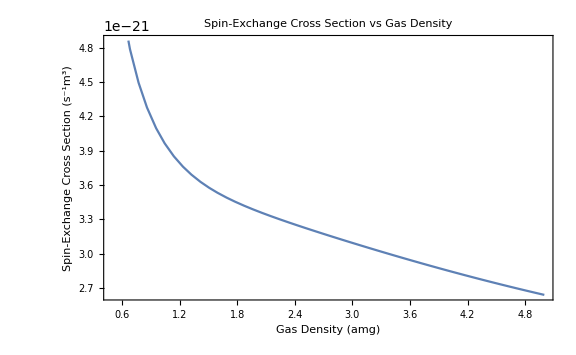

```mathematica
Plot[SpinExchange[0.01, 0.10, 0.89,383,G,0.95], {G, 0.5,5}, Frame->True, FrameLabel->{"Gas Density (amg)", "Spin-Exchange Cross Section (s^-1m^3)"}, PlotLabel-> "Spin-Exchange Cross Section vs Gas Density", ImageSize-> Large]
```

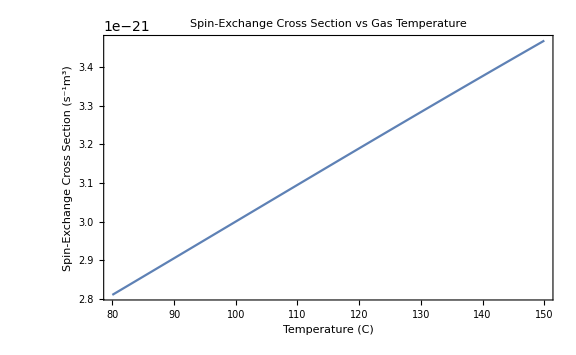

```mathematica
Plot[SpinExchange[0.01, 0.10, 0.89,273+T,3,0.95], {T, 80,150},Frame->True, FrameLabel->{"Temperature (C)", "Spin-Exchange Cross Section (s^-1m^3)"}, PlotLabel-> "Spin-Exchange Cross Section vs Gas Temperature", ImageSize-> Large]
```

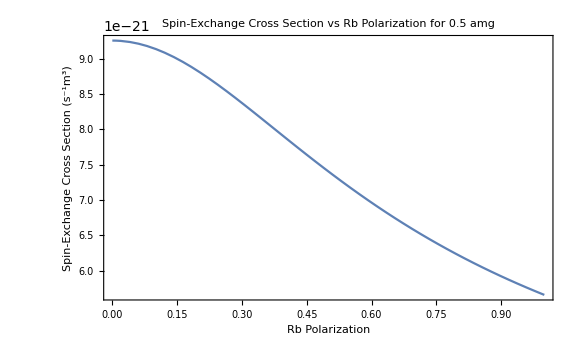

```mathematica
Plot[SpinExchange[0.01, 0.10, 0.89,383,0.5,P], {P, 0,1}, Frame->True, FrameLabel->{"Rb Polarization", "Spin-Exchange Cross Section (s^-1m^3)"}, PlotLabel-> "Spin-Exchange Cross Section vs Rb Polarization for 0.5 amg", ImageSize-> Large] (*for low densities, where Subscript[f, s]=0 the spin-exchange cross section has a large dependency on the Rb polarization*)
```

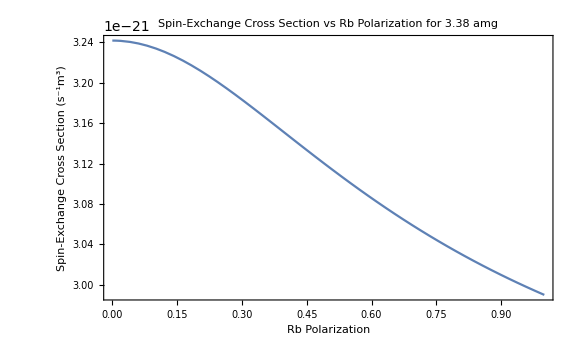

```mathematica
Plot[SpinExchange[0.01, 0.10, 0.89,383,3.38,P], {P, 0,1},Frame->True, FrameLabel->{"Rb Polarization", "Spin-Exchange Cross Section (s^-1m^3)"}, PlotLabel-> "Spin-Exchange Cross Section vs Rb Polarization for 3.38 amg", ImageSize-> Large](*for higher densities, where Subscript[f, s]≠ 0 the spin-exchange cross section has a minimal dependency on the Rb polarization*)
```

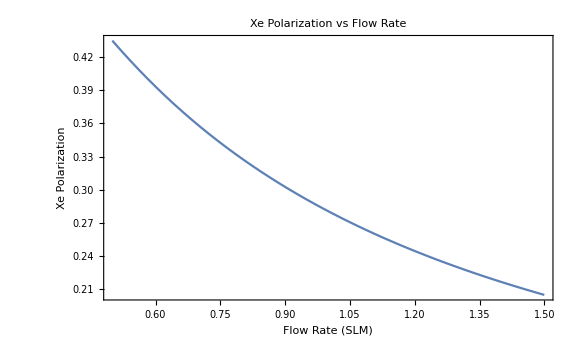

```mathematica
Plot[XePolarization[0.01, 0.10, 0.89,383,3,0.95,3*10^18,0.003,0.270,slm,25], {slm, 0.5,1.5}, Frame->True, FrameLabel->{"Flow Rate (SLM)", "Xe Polarization"}, PlotLabel-> "Xe Polarization vs Flow Rate", ImageSize-> Large]
```

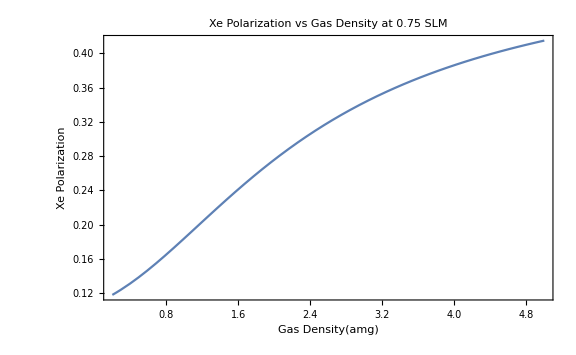

```mathematica
Plot[XePolarization[0.01, 0.10, 0.89,383,G,0.95,3*10^18,0.003,0.270,0.75,25], {G, 0.2,5}, Frame->True, FrameLabel->{"Gas Density(amg)", "Xe Polarization"}, PlotLabel-> "Xe Polarization vs Gas Density at 0.75 SLM", ImageSize-> Large]
```

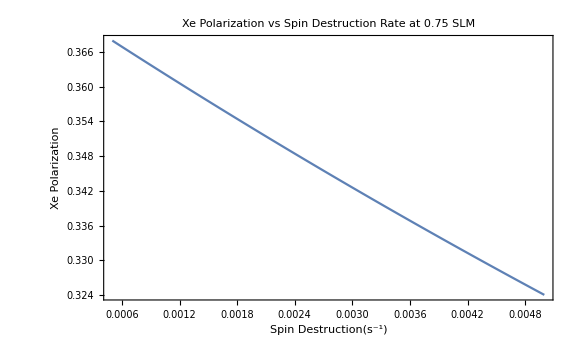

```mathematica
Plot[XePolarization[0.01, 0.10, 0.89,383,3,0.95,3*10^18,SD,0.27 ,0.75,25], {SD, 0.0005,0.005},Frame->True, FrameLabel->{"Spin Destruction(s^-1)", "Xe Polarization"}, PlotLabel-> "Xe Polarization vs Spin Destruction Rate at 0.75 SLM", ImageSize-> Large]
```

### Neat Examples

If the Rb Polarization is known as an approximate function of the Rb vapor density, it can be used inside this function to find the optimal Rb vapor density.

-Graphics-

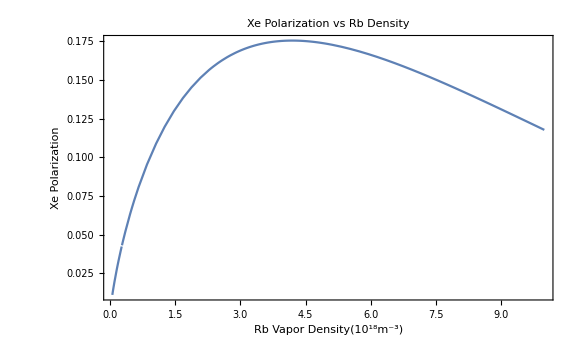

```mathematica
PRb[nRb_]:= 10.311-0.232Log[nRb]; (*example definition of polarization as function of Rb vapor density. This is what was measured for our system with a 36 W laser (300 ml optical cell)*)
Plot[PRb[nRb], {nRb,5*10^17, 5*10^18}, Frame->True, FrameLabel-> {"Rb Vapor Density (10^18m^-3)", "Rb Polarization"}, PlotLabel-> "Rb Polarization vs Rb Density"]
Plot[XePolarization[0.01, 0.10, 0.89,383,3,PRb[nrb*10^18],nrb*10^18,0.003,0.280,0.75,25], {nrb, 0.05,10},Frame->True, FrameLabel->{"Rb Vapor Density(10^18m^-3)", "Xe Polarization"}, PlotLabel-> "Xe Polarization vs Rb Density", ImageSize-> Large]
```

We can use the NMaximize function to find the optimal Rb density for our system. Note that this will be dependent on flow rate.

```mathematica
NMaximize[{XePolarization[0.01, 0.10, 0.89,383,3,PRb[nrb],nrb,0.0045,0.280,0.75,25],1*10^17≤ nrb≤ 1*10^19}, nrb] (*flow rate = 0.75 SLM*)
```

{0.172625,{nrb→4.15316×10^18}}

```mathematica
NMaximize[{XePolarization[0.01, 0.10, 0.89,383,3,PRb[nrb],nrb,0.0045,0.280,0.5,25],1*10^17≤ nrb≤ 1*10^19}, nrb](*flow rate = 0.5 SLM*)
```

{0.206809,{nrb→3.4924×10^18}}

### A bit more fun...

```mathematica
Manipulate[Plot[SpinExchange[0.01, 0.10, 0.89,273+T,G,0.95], {G, 0.25, 5}, Frame->True, FrameLabel->{"Gas Density (amg)", "Spin-Exchange Cross Section (s^-1m^3)"}, PlotLabel-> "Spin-Exchange Cross Section vs Gas Temperature", ImageSize-> Large], {T, 80, 160, 2}]
```